```mathematica
SetDirectory["/Users/cdschillaci/Desktop/Efimov in a Well/BH C++ Code/data"];
```

```mathematica
eMin=0; eMax=8.5;
aInvMin=0;aInvMax=0;

aScale[x_]:=Sign[x]x^2;
eScale[x_]:=x;


rawData=Import[StringJoin["PairsByA.csv"]];
rawData=Sort[rawData,#1[[1]]<#2[[1]]&];
ee={};

result={};

Off[Part::partw];
For[rawIndex=1,rawIndex≤Length[rawData],rawIndex++,

AppendTo[ee,{rawData[[rawIndex,2]],rawData[[rawIndex,3]]}];

(* When all e for a given aInv have been loaded, do some work *)
(* Also does work when it arrives at the end of the list rawData *)
If[rawData[[rawIndex,1]]!=rawData[[rawIndex+1,1]]||rawIndex==Length[rawData],

(* interpolate the {energy,eigenvalue} data *)
f=Interpolation[ee];

(* find the set of eigenvalues within 0.03 of 1 as a set of guesses for the root solver *)
eclose={};
Do[
If[Abs[ee[[i,2]]-1.0]<.2,AppendTo[eclose,ee[[i,1]]]],
{i,1,Length[ee]}
];

(* use the values saved in eclose and the interpolated data to find the energies at which an eigenvalue of mm=1. Save these to "es" *)
es={};
AppendTo[es,FindRoot[f[x]-1==0,{x,eclose[[1]]}][[1,2]]];
Do[
answer=FindRoot[f[x]-1==0,{ x,eclose[[i]] }][[1,2]];
If[Abs[answer-es[[Dimensions[es][[1]]]]]>.001,AppendTo[es,answer]],
{i,2,Dimensions[eclose][[1]]}
];

(* now append the interpolated energy eigenvalues as pairs {1/a,energy} to the table "result" *)
Do[
AppendTo[result,{aScale[rawData[[rawIndex,1]]],eScale[es[[i]]]}],
{i,1,Dimensions[es][[1]]}
];

(* reset "ee" *)
ee={};
];
];
```

```mathematica
result
```

{{0,7.83531},{0,7.46527},{0,6.14172},{0,5.46523},{0,3.9888},{0,1.71496},{0,8.24835}}

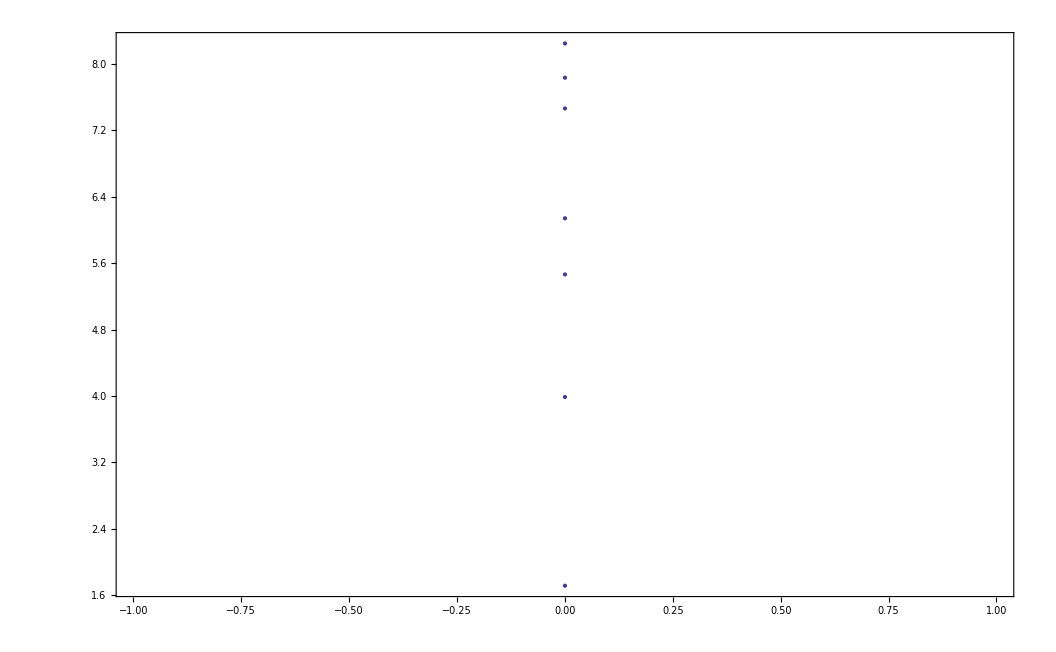

```mathematica
ListPlot[result,Frame->True]
```

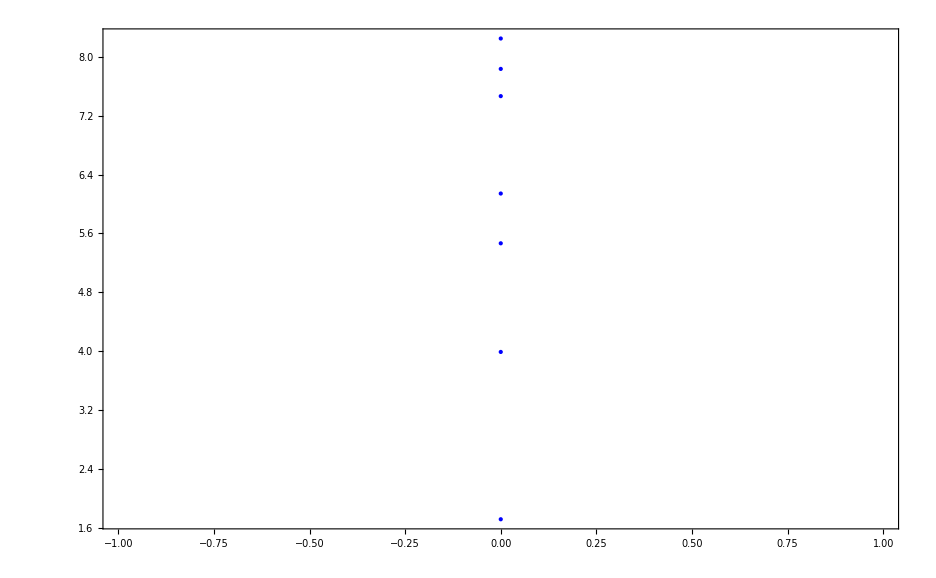

```mathematica
ListPlot[{EfimovianPairs,UniversalPairs,result},Frame->True,PlotStyle->{Directive[Red,PointSize[Large]],Directive[Green,PointSize[Large]],Directive[Blue,PointSize[Medium]]},PlotRange->{0,15}]
```

```mathematica
ToExport=Table[ListPlot[allResults[Λ],Frame->True,"ImageSize"->Large,FrameLabel->{"1/a","k"},PlotRange->{{aScale[aInvMin],aScale[aInvMax]},{eScale[eMin],eScale[eMax]}}],{Λ,Λmin,Λmax,Λstep}];
Export["Renormalizing.mov",%,"FrameRate"->1.2,ImageSize->1400];
```

```mathematica
(*For[Λ=Λmin,Λ≤Λmax,Λ+=Λstep,
Export[StringJoin["InterpolatedPairs/InterpolatedPairsAtLambda",ToString[Λ],".csv"],allResults[Λ]]];*)
```

```mathematica
GroupedEnergies[Λ_,nLevels_]:=Module[{},
close=.25;

temp=Sort[allResults[Λ],#1[[1]]*10^6+#1[[2]]<#2[[1]]*10^6+#2[[2]]&];
currentElist={};
Do[energies[Λ,n]={},{n,1,nLevels}];

Do[
AppendTo[currentElist,temp[[i,2]]];

If[temp[[i,1]]!=temp[[i+1,1]],
offset=0;
Do[
If[temp[[i,1]]==temp[[1,1]]||currentElist[[j-offset]]<energies[Λ,j][[Length[energies[Λ,j]],2]],
AppendTo[energies[Λ,j],{temp[[i,1]],currentElist[[j-offset]]}],offset+=1]
,{j,1,nLevels}];
currentElist={};
]

,{i,1,Length[temp]}];
];
(*GroupedEnergies[10,4]
ListPlot[{energies[10,1],energies[10,2],energies[10,3],energies[10,4]},Joined->True]*)
```

```mathematica
result
```

{{0,7.83531},{0,7.46527},{0,6.14172},{0,5.46523},{0,3.9888},{0,1.71496},{0,8.24835}}